```mathematica
aa1=31/9Nc-10/9nf;
beta0=11/3*Nc-2/3*nf;
CF=4/3;
Nc=3;
nf=4;
VB=alpha CF;
mu=4*alpha;
```

```mathematica
Rprime[r_,alpha_]:=r*Exp[EulerGamma]*4*alpha;
VV[r_,L_,n_,alpha_]:=(*(Nc-1)/(Nc+1)*alpha CF/(r-n*L)*(1(*+alpha/(4*Pi)*(2*beta0*Log[Rprime[r-n*L,alpha]]+aa1)*))*)-1*alpha CF/(r-n*L)*(1(*+alpha/(4*Pi)*(2*beta0*Log[Rprime[r-n*L,alpha]]+aa1)*));
```

```mathematica
VV[r_,L_,n_,alpha_]:=(Nc-1)/(Nc+1)*alpha CF/(r-n*L)*(1+alpha/(4*Pi)*(2*beta0*Log[Rprime[r-n*L,alpha]]+aa1))-1*alpha CF/(r-n*L)*(1+alpha/(4*Pi)*(2*beta0*Log[Rprime[r-n*L,alpha]]+aa1));
```

```mathematica
VV[2,10,0,0.1]
```

-0.0364608

```mathematica
Sum[VV[r,.02,n,0.1],{n,-1,1}]
```

-0.133333/(r+0.)-0.133333/(r+0.02)-0.133333/(r-0.02)

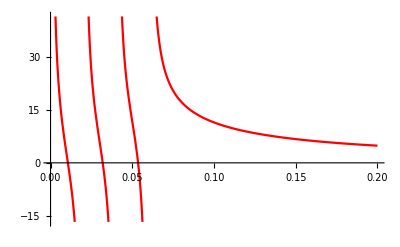

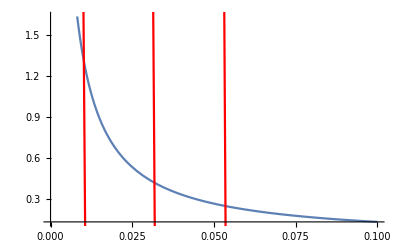

```mathematica
tInf=Plot[-VV[r,.02,0,0.01],{r,0,.1},PlotRange->Automatic];
tFin=Plot[-Sum[VV[r,.02,n,0.1],{n,-3,3}],{r,0,.2},PlotRange->Automatic,PlotStyle->Red]
Show[tInf,tFin]
```